# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-22

```mathematica
countries=Union[seqData[[All,2]]]
```

{Argentina,Australia,Brazil,Canada,Chile,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Singapore,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Argentina,Australia,Brazil,Canada,Chile,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Singapore,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Argentina→{{2022-01-08,23},{2022-01-09,5},{2022-01-10,29},{2022-01-11,20},{2022-01-12,17},{2022-01-13,16},{2022-01-14,6},{2022-01-15,3},{2022-01-16,4},{2022-01-17,11},{2022-01-18,8},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Australia→{{2022-01-08,87},{2022-01-09,146},{2022-01-10,119},{2022-01-11,119},{2022-01-12,112},{2022-01-13,142},{2022-01-14,109},{2022-01-15,71},{2022-01-16,60},{2022-01-17,69},{2022-01-18,43},{2022-01-19,24},{2022-01-20,12},{2022-01-21,6},{2022-01-22,10}},Brazil→{{2022-01-08,114},{2022-01-09,86},{2022-01-10,200},{2022-01-11,174},{2022-01-12,109},{2022-01-13,67},{2022-01-14,18},{2022-01-15,8},{2022-01-16,8},{2022-01-17,13},{2022-01-18,3},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Canada→{{2022-01-08,188},{2022-01-09,103},{2022-01-10,105},{2022-01-11,54},{2022-01-12,109},{2022-01-13,36},{2022-01-14,7},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Chile→{{2022-01-08,18},{2022-01-09,35},{2022-01-10,56},{2022-01-11,23},{2022-01-12,8},{2022-01-13,10},{2022-01-14,6},{2022-01-15,0},{2022-01-16,0},{2022-01-17,20},{2022-01-18,10},{2022-01-19,12},{2022-01-20,6},{2022-01-21,0},{2022-01-22,0}},Croatia→{{2022-01-08,1},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Denmark→{{2022-01-08,779},{2022-01-09,519},{2022-01-10,1539},{2022-01-11,1979},{2022-01-12,1639},{2022-01-13,1995},{2022-01-14,2039},{2022-01-15,1585},{2022-01-16,1380},{2022-01-17,2024},{2022-01-18,2241},{2022-01-19,1939},{2022-01-20,1666},{2022-01-21,1911},{2022-01-22,1596}},France→{{2022-01-08,82},{2022-01-09,120},{2022-01-10,762},{2022-01-11,90},{2022-01-12,22},{2022-01-13,23},{2022-01-14,40},{2022-01-15,50},{2022-01-16,45},{2022-01-17,178},{2022-01-18,55},{2022-01-19,4},{2022-01-20,1},{2022-01-21,0},{2022-01-22,0}},Germany→{{2022-01-08,942},{2022-01-09,252},{2022-01-10,2094},{2022-01-11,2082},{2022-01-12,1410},{2022-01-13,1236},{2022-01-14,1295},{2022-01-15,599},{2022-01-16,202},{2022-01-17,950},{2022-01-18,1345},{2022-01-19,194},{2022-01-20,85},{2022-01-21,2},{2022-01-22,8}},India→{{2022-01-08,47},{2022-01-09,27},{2022-01-10,40},{2022-01-11,34},{2022-01-12,21},{2022-01-13,27},{2022-01-14,33},{2022-01-15,66},{2022-01-16,45},{2022-01-17,25},{2022-01-18,6},{2022-01-19,8},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Ireland→{{2022-01-08,2},{2022-01-09,2},{2022-01-10,6},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Israel→{{2022-01-08,35},{2022-01-09,144},{2022-01-10,332},{2022-01-11,267},{2022-01-12,130},{2022-01-13,75},{2022-01-14,37},{2022-01-15,23},{2022-01-16,62},{2022-01-17,57},{2022-01-18,15},{2022-01-19,83},{2022-01-20,138},{2022-01-21,0},{2022-01-22,0}},Japan→{{2022-01-08,832},{2022-01-09,103},{2022-01-10,84},{2022-01-11,17},{2022-01-12,27},{2022-01-13,26},{2022-01-14,20},{2022-01-15,6},{2022-01-16,4},{2022-01-17,8},{2022-01-18,8},{2022-01-19,7},{2022-01-20,2},{2022-01-21,0},{2022-01-22,0}},Lithuania→{{2022-01-08,1},{2022-01-09,0},{2022-01-10,0},{2022-01-11,14},{2022-01-12,5},{2022-01-13,11},{2022-01-14,13},{2022-01-15,4},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Netherlands→{{2022-01-08,184},{2022-01-09,180},{2022-01-10,264},{2022-01-11,180},{2022-01-12,147},{2022-01-13,129},{2022-01-14,95},{2022-01-15,44},{2022-01-16,52},{2022-01-17,20},{2022-01-18,7},{2022-01-19,47},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},New Zealand→{{2022-01-08,27},{2022-01-09,26},{2022-01-10,51},{2022-01-11,27},{2022-01-12,47},{2022-01-13,34},{2022-01-14,22},{2022-01-15,49},{2022-01-16,39},{2022-01-17,67},{2022-01-18,17},{2022-01-19,21},{2022-01-20,16},{2022-01-21,0},{2022-01-22,0}},Norway→{{2022-01-08,12},{2022-01-09,21},{2022-01-10,41},{2022-01-11,134},{2022-01-12,10},{2022-01-13,12},{2022-01-14,11},{2022-01-15,7},{2022-01-16,50},{2022-01-17,18},{2022-01-18,14},{2022-01-19,13},{2022-01-20,11},{2022-01-21,0},{2022-01-22,0}},Singapore→{{2022-01-08,40},{2022-01-09,38},{2022-01-10,80},{2022-01-11,60},{2022-01-12,42},{2022-01-13,55},{2022-01-14,52},{2022-01-15,54},{2022-01-16,55},{2022-01-17,14},{2022-01-18,40},{2022-01-19,33},{2022-01-20,42},{2022-01-21,0},{2022-01-22,0}},South Africa→{{2022-01-08,26},{2022-01-09,19},{2022-01-10,18},{2022-01-11,28},{2022-01-12,21},{2022-01-13,11},{2022-01-14,12},{2022-01-15,3},{2022-01-16,5},{2022-01-17,6},{2022-01-18,10},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},South Korea→{{2022-01-08,67},{2022-01-09,78},{2022-01-10,79},{2022-01-11,13},{2022-01-12,12},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},Spain→{{2022-01-08,93},{2022-01-09,67},{2022-01-10,181},{2022-01-11,229},{2022-01-12,257},{2022-01-13,169},{2022-01-14,171},{2022-01-15,48},{2022-01-16,28},{2022-01-17,29},{2022-01-18,10},{2022-01-19,12},{2022-01-20,15},{2022-01-21,0},{2022-01-22,0}},Sweden→{{2022-01-08,61},{2022-01-09,126},{2022-01-10,211},{2022-01-11,89},{2022-01-12,88},{2022-01-13,191},{2022-01-14,118},{2022-01-15,39},{2022-01-16,31},{2022-01-17,44},{2022-01-18,15},{2022-01-19,10},{2022-01-20,5},{2022-01-21,0},{2022-01-22,0}},Switzerland→{{2022-01-08,214},{2022-01-09,219},{2022-01-10,695},{2022-01-11,576},{2022-01-12,323},{2022-01-13,162},{2022-01-14,149},{2022-01-15,85},{2022-01-16,168},{2022-01-17,371},{2022-01-18,171},{2022-01-19,93},{2022-01-20,13},{2022-01-21,0},{2022-01-22,0}},Thailand→{{2022-01-08,38},{2022-01-09,21},{2022-01-10,42},{2022-01-11,2},{2022-01-12,20},{2022-01-13,11},{2022-01-14,26},{2022-01-15,9},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0}},United Kingdom→{{2022-01-08,5988},{2022-01-09,4793},{2022-01-10,8548},{2022-01-11,8463},{2022-01-12,6664},{2022-01-13,6581},{2022-01-14,8098},{2022-01-15,5653},{2022-01-16,5404},{2022-01-17,8430},{2022-01-18,8280},{2022-01-19,7824},{2022-01-20,7126},{2022-01-21,9078},{2022-01-22,4479}},USA→{{2022-01-08,4273},{2022-01-09,4286},{2022-01-10,7486},{2022-01-11,7086},{2022-01-12,5108},{2022-01-13,3452},{2022-01-14,2714},{2022-01-15,1567},{2022-01-16,1154},{2022-01-17,3214},{2022-01-18,3024},{2022-01-19,1675},{2022-01-20,1084},{2022-01-21,0},{2022-01-22,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

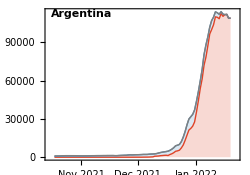
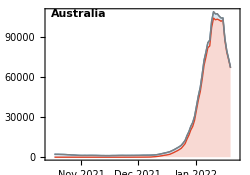
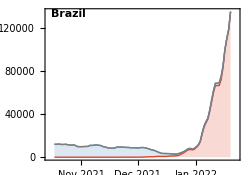
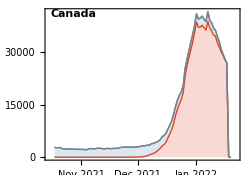
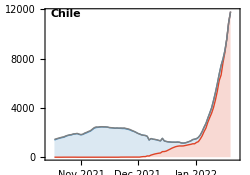
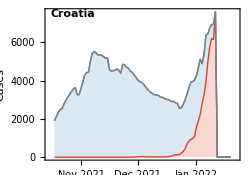
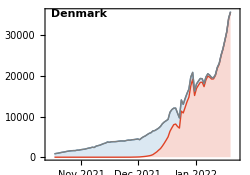
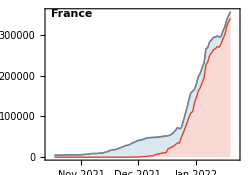
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png